```mathematica
h[s_]:=Evaluate[Integrate[Sqrt[1/Sqrt[1-t^2]]*Exp[-I*t*s],{t,-1,1}]]
```

```mathematica
h[s]
```

√π Gamma[3/4] Hypergeometric0F1Regularized[5/4,-s^2/4]

```mathematica
Simplify[h[s]]
```

√π Gamma[3/4] Hypergeometric0F1Regularized[5/4,-s^2/4]

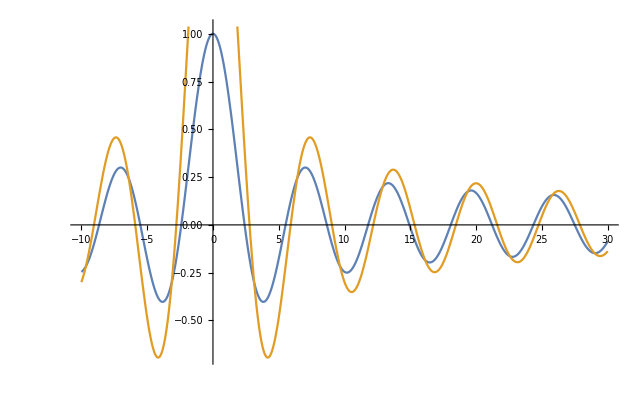

```mathematica
Plot[{BesselJ[0,s],h[s]},{s,-10,30}]
```

```mathematica
alsoh[s_]:=Pi^(1/2)*Gamma[3/4]*BesselJ[1/4,s]*2^(1/4)/s^(1/4)
```

```mathematica
Integrate[alsoh[s]*Exp[I*s*t],{s,-Infinity,Infinity}]
```

ConditionalExpression[0,Im[t]==0&&(Re[t]<-1||Re[t]>1)]

```mathematica
Integrate[alsoh[s],{s,0,s}]
```

ConditionalExpression[(√π s Gamma[3/4] HypergeometricPFQ[{1/2},{5/4,3/2},-s^2/4])/Gamma[5/4],Re[s]>0||(Re[s]≥0&&Im[s]>0)]

```mathematica
h[2.3]
```

0.512517

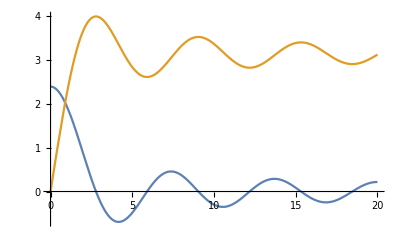

```mathematica
Plot[{alsoh[s],(√π s Gamma[3/4] HypergeometricPFQ[{1/2},{5/4,3/2},-s^2/4])/Gamma[5/4]},{s,0,20}]
```